# FitzHugh-Nagumo model

#### Constant stimulation

```mathematica
eqV[V_,w_]:=1/ϵ*(-w + V*(1-V)*(V-a)+Iext)
eqw[V_,w_]:=V-γ*w
```

```mathematica
eql = SolveValues[{eqV[V, w] == 0.0, eqw[V, w] == 0.0}/.{a->0.2, γ->0.4, ϵ->0.001}, {V, w}, Reals]
J = D[{eqV[V, w], eqw[V, w]}, {{V, w}}]/.{a->0.2, γ->0.4, ϵ->0.001}
re = Real[Eigenvalues[J/.{V->eql[[1,1]], w->eql[[1,2]]}]]
```

SolveValues::ratnz: SolveValues was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.4 Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1],Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]}}

{{1000. ((1-V) (-0.2+V)+(1-V) V-(-0.2+V) V),-1000.},{1,-0.4}}

Real[{1/2 (-200.4+960. Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]-480. Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]^2-√(35840.2-383232. Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]+1.11322×10^6 Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]^2-921600. Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]^3+230400. Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]^4)),1/2 (-200.4+960. Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]-480. Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]^2+√(35840.2-383232. Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]+1.11322×10^6 Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]^2-921600. Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]^3+230400. Root[-125. Iext+135. #1-24. #1^2+8. #1^3&,1]^4))}]

{{V→0.116563,w→0.291408}}

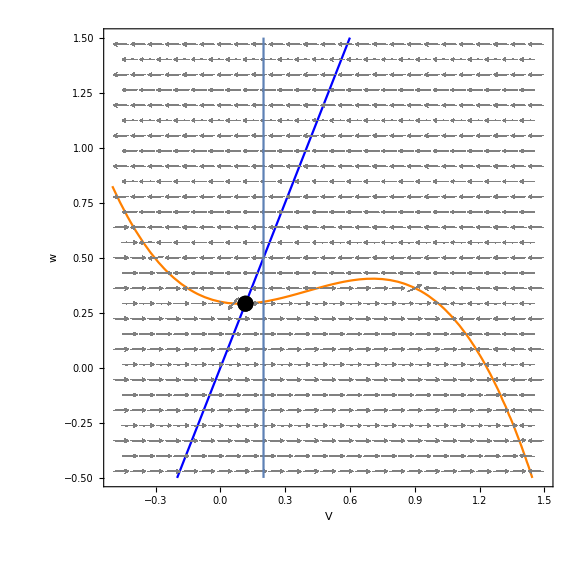

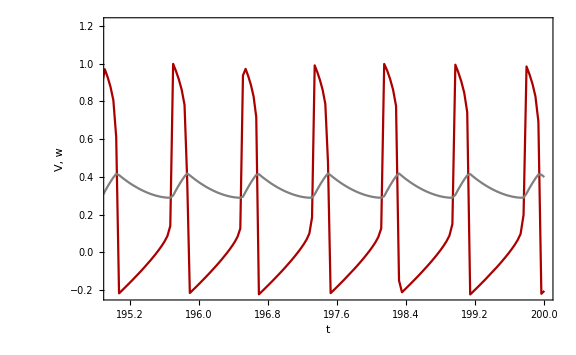

```mathematica
pars={a->0.2,γ->0.4,ϵ->0.001, Iext->0.3};
eql = NSolve[{eqV[V, w] == 0.0, eqw[V, w] == 0.0} /. pars, {V, w}, Reals]

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tmin= 100.0;
tmax = 200;
init = Thread[{V[tmin], w[tmin]} == {0.0,0.0} ];
solution = NDSolve[{sys, init}, vars, {t, tmin, tmax}];

timePlot = Plot[Evaluate[vars /. solution], {t, tmin, tmax}, PlotRange -> {{195, 200}, All}, PlotStyle ->{Darker[Red],Gray},Frame -> True, FrameLabel -> {"t", "V, w"}, ImageSize->Large];

minV = -0.5; maxV = 1.5; minw = -0.5; maxw = 1.5;
(* draw null clines *)
nullClines = ContourPlot[{(eqV[V, w] /. pars) == 0, (eqw[V, w] /. pars) == 0}, {V, minV, maxV}, {w, minw, maxw},
 Frame -> True, FrameLabel -> {"V", "w"}, AspectRatio -> 1, ContourStyle -> {Orange, Blue}];
 (* draw vector field *)
vectorField = VectorPlot[{eqV[V, w], eqw[V, w] } /. pars, {V, minV, maxV}, {w,minw, maxw}, VectorStyle -> {Gray,"PinDart"}, VectorColorFunction->None, VectorPoints -> Fine];
(*equilibrium point*)
eqlPlot = ListPlot[{V, w} /. eql, PlotStyle -> {{Black, PointSize[0.02]}}, Frame -> True, FrameLabel -> {"V", "w"}, AspectRatio -> 1];
(*threshold*)
aPlot = ListLinePlot[{{a/.pars, minw}, {a/.pars, maxw}}];

Show[nullClines, vectorField, eqlPlot, aPlot, ImageSize->Large]
Show[timePlot]
```

#### Periodic stimulation

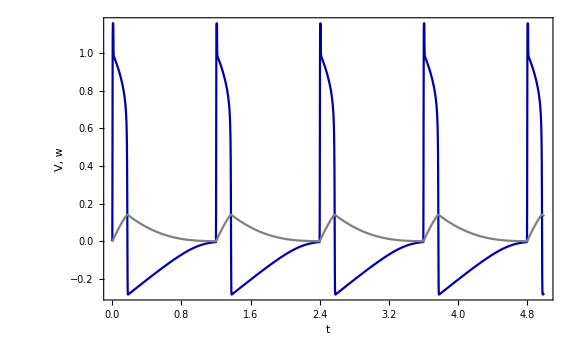

```mathematica
stimuliTrain[t_, A_,duty_, period_]:=A*UnitBox[Mod[t/period,1.]/(2. duty)];
Iext = stimuliTrain[t, 0.2, 0.01, 1.2];
eqV[V_,w_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext)
eqw[V_,w_]:=V-γ*w
pars={a->0.1,γ->0.5,ϵ->0.001};

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tmin= 0.0;
tmax = 5;
init = Thread[{V[tmin], w[tmin]} == {0.0,0.0} ];
solution = NDSolve[Join[sys, init], vars, {t, tmin, tmax}];
Plot[Evaluate[vars /. solution], {t, tmin, tmax}, PlotRange -> {All, All}, PlotStyle ->{Darker[Blue],Gray},Frame -> True, FrameLabel -> {"t", "V, w"}, ImageSize->Large]
```

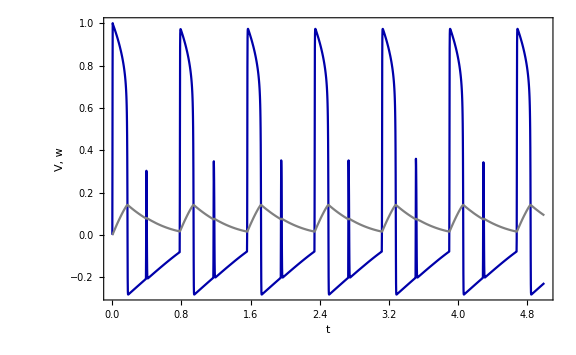

```mathematica
stimuliTrain[t_, A_,duty_, period_]:=A*UnitBox[Mod[t/period,1.]/(2. duty)];
Iext = stimuliTrain[t, 0.2, 0.01, 0.39];
eqV[V_,w_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext)
eqw[V_,w_]:=V-γ*w
pars={a->0.1,γ->0.5,ϵ->0.001};

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tmin= 0;
tmax = 5;
init = Thread[{V[tmin], w[tmin]} == {0.0,0.0} ];
solution = NDSolve[Join[sys, init], vars, {t, tmin, tmax}];
Plot[Evaluate[vars /. solution], {t, tmin, tmax}, PlotRange -> {All, All}, PlotStyle ->{Darker[Blue],Gray},Frame -> True, FrameLabel -> {"t", "V, w"}, ImageSize->Large]
```

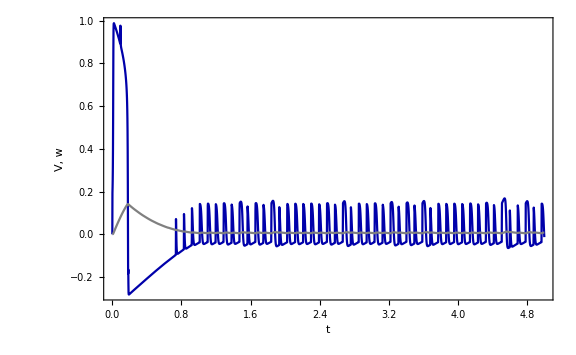

```mathematica
stimuliTrain[t_, A_,duty_, period_]:=A*UnitBox[Mod[t/period,1.]/(2. duty)];
Iext = stimuliTrain[t, 0.2, 0.01, 0.092];
eqV[V_,w_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext)
eqw[V_,w_]:=V-γ*w
pars={a->0.1,γ->0.5,ϵ->0.001};

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]} /. pars;
vars = {V[t], w[t]};
tmin= 0;
tmax = 5;
init = Thread[{V[tmin], w[tmin]} == {0.0,0.0} ];
solution = NDSolve[Join[sys, init], vars, {t, tmin, tmax}];
Plot[Evaluate[vars /. solution], {t, tmin, tmax}, PlotRange -> {All, All}, PlotStyle ->{Darker[Blue],Gray},Frame -> True, FrameLabel -> {"t", "V, w"}, ImageSize->Large]
```

```mathematica
tmp=Reap[NDSolve[{D[x[t],t]==-y[t],D[y[t],t]==x[t],x[0]==1,y[0]==0,WhenEvent[x[t]==0, Sow[t]]},{x,y},{t,0,20}]]
sol=tmp[[1,1]]
pts=ListConvolve[{1,-1},tmp[[2,1]]]
```

{{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}},{{1.5708,4.71239,7.85398,10.9956,14.1372,17.2788}}}

{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}

{3.14159,3.14159,3.14159,3.14159,3.14159}

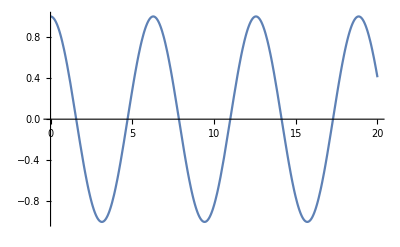

```mathematica
Plot[x[t]/.sol,{t,0,20}]
```

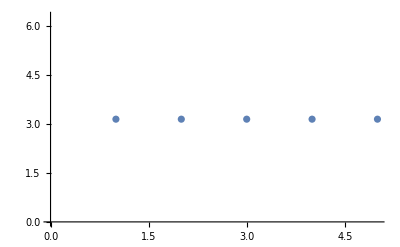

```mathematica
ListPlot[pts]
```

```mathematica
ls={k, b, c, d, e, f}
Pick[ls,Table[Mod[i,2],{i,1,Length@ls}],1]
```

{k,b,c,d,e,f}

{k,c,e}